```mathematica
bookName="Banham";
bookSel=MeteoraBookSelect[bookName];
data=XenothekaTextImport@bookSel[[2]];
```

```mathematica
data1=StringReplace[data,{"\n"->" ","\""->"'"}];
data2=ToLowerCase@data1;
words=TextWords@data2;
words1=DeleteStopwords@words;
$MeteoraWordData=Uncompress@Import[CloudObject["https://www.wolframcloud.com/obj/hovestadt/Published/METEORA DATASETS/MeteoraWordData"],"Text"];
nouns=Select[words1,MeteoraWordNounQ];
stems=MeteoraWordStem/@nouns;
dict=Sort@DeleteDuplicates[stems];
freqs=Reverse@SortBy[Normal@Counts@stems,Last];
paragraphs=StringSplit[data,"\n"];
paragraphs=MapIndexed[{bookName,First@#2}->#1&,paragraphs];
paragraphs1=MeteoraParagraphsBrokenJoin[paragraphs];
sentences=Flatten@Cases[paragraphs1[[1;;-1]],(_List->a_String):>Select[TextSentences@a,StringLength[#]>60&],All];
```

```mathematica
paragraphs2=Flatten[MeteoraParagraphTooLargeSplit/@paragraphs1];
paragraphs3=Select[paragraphs2,StringLength@#[[2]]>100&];
fe=FeatureExtraction[paragraphs3[[All,2]],{"LowerCasedText","WordVectors"}];
dr=DimensionReduction[Normal@fe@paragraphs3[[All,2]],30];
pv=MapIndexed[#1->First@#2&,dr/@fe@paragraphs3[[All,2]]];
```

```mathematica
nm =NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]
```

EmbeddingLayer[<>]

```mathematica
DeleteObject[ResourceObject["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]]
```

```mathematica
ptsOfWords=nm["One can almost say that the only serious attempt to cope with this situation that achieved any widespread distribution is the inglenook, virtually a room within the room, around the fireplaces of rooms in large houses by Frank Lloyd Wright, C. F. A. Voysey and their contemporaries. These screened areas with built-in seats provided an area of reliable thermal performance, shielded from draughts. Though ultimately a revival of mediaeval usage, they could only be properly revived in a epoch that already disposed of piped central heating—the effect of trapping so much of the heat available in an area around the fire would have been to deprive the rest of the room thermally, were background heat not available."];
```

```mathematica
ptsOfWords2D=DimensionReduce[ptsOfWords,2]
```

{{2.48452,-0.585823},{0.891899,-6.48162},{-0.176803,-1.31315},{1.86505,-4.56138},{4.01315,-2.57523},{3.51245,2.48928},{1.63669,-2.87175},{-0.533309,-1.71623},{-0.1264,-0.904639},{3.34744,-2.98156},{-3.35588,-1.93501},{2.303,0.470448},{2.76764,-1.81694},{0.416363,-2.19059},{4.01315,-2.57523},{-2.49599,-1.15245},{1.3364,-3.00286},{-1.44769,1.48144},{-2.85076,1.67611},{2.75069,-1.41243},{3.51245,2.48928},{-8.59007,2.41533},{3.28262,-0.221304},{-2.62316,-1.86968},{1.9158,-0.0856227},{-3.27575,-0.167715},{-0.885097,2.04595},{3.51245,2.48928},{-3.27575,-0.167715},{3.28262,-0.221304},{0.73356,1.40448},{3.51245,2.48928},{-8.15305,1.94853},{4.06376,6.18754},{-5.51177,0.891494},{3.24232,2.19235},{-0.986466,1.42655},{-2.63235,2.59273},{1.50074,1.10907},{-2.43904,-0.431226},{-2.76524,0.113893},{-2.86251,-0.625593},{3.28262,-0.221304},{-3.72584,0.0098601},{2.4413,-1.4349},{-3.97944,-1.52226},{2.4413,-1.4349},{1.9158,-0.0856227},{2.4413,-1.4349},{-8.27839,0.437626},{3.1872,0.0707032},{2.74998,-0.323465},{-4.01581,0.91946},{2.4413,-1.4349},{0.698225,-2.11537},{-5.2324,-1.07039},{-0.0850075,1.805},{2.303,0.470448},{-2.93974,2.10387},{2.35575,-0.0810715},{3.24232,2.19235},{-1.00618,-0.0146832},{-2.27394,-0.747747},{3.8945,0.479004},{-0.0475967,2.49007},{4.06376,6.18754},{-4.11269,-2.45866},{-6.9365,2.91676},{-1.55229,-0.578795},{3.28262,-0.221304},{-6.01123,0.399779},{2.31014,2.58379},{-7.38466,1.42018},{2.4413,-1.4349},{0.124664,-2.57795},{-1.43573,-2.67612},{1.9158,-0.0856227},{-3.82587,2.66499},{4.06376,6.18754},{-6.65327,4.38743},{-4.79213,0.444652},{3.28262,-0.221304},{3.24727,-4.62367},{1.94756,-5.53181},{1.63669,-2.87175},{2.60327,-5.45087},{-3.59778,-4.7465},{-4.07489,-0.0336445},{3.24232,2.19235},{1.9158,-0.0856227},{-5.30269,2.4508},{4.01315,-2.57523},{0.640654,-1.68194},{-4.62234,-1.29499},{4.06376,6.18754},{-7.20687,0.858295},{1.0302,4.57416},{-5.81834,1.22751},{-1.46733,0.32998},{3.51245,2.48928},{-1.52019,-1.21982},{4.06376,6.18754},{-5.76568,2.22647},{1.41923,-4.39361},{0.809663,-1.43046},{4.06376,6.18754},{3.51245,2.48928},{-3.6529,-0.341282},{-2.60987,-3.20801},{3.24232,2.19235},{3.8945,0.479004},{-0.0475967,2.49007},{0.73356,1.40448},{3.51245,2.48928},{-1.44693,0.39688},{2.98842,-5.11924},{3.21812,-4.13096},{2.33236,-2.34613},{3.34744,-2.98156},{-3.41423,-0.570532},{3.51245,2.48928},{-1.04558,-0.6451},{4.06376,6.18754},{3.51245,2.48928},{-3.27575,-0.167715},{-8.7991,-1.19997},{3.28262,-0.221304},{2.63805,-0.857197},{-3.00855,0.352854},{-3.6529,-0.341282},{2.99692,-5.69954},{-2.60987,-3.20801},{2.4413,-1.4349}}

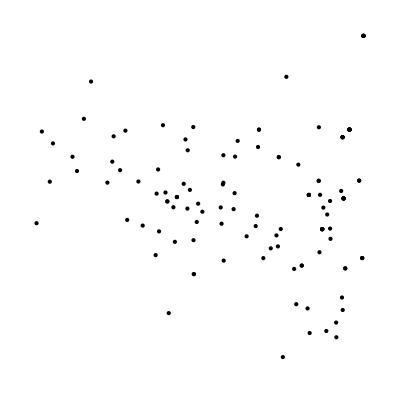

```mathematica
Graphics[{Point@ptsOfWords2D}]
```

```mathematica
dr=DimensionReduction[Normal@fe@paragraphs3[[All,2]],3]
```

DimensionReducerFunction[…]

```mathematica
Graphics3D[{Point@(dr@fe@paragraphs3[[All,2]])}]
```

-Graphics3D-

```mathematica
pts = RandomReal[1,{120,3}];
```

```mathematica
RGBColor/@pts
```

{RGBColor[{0.4414383479355306, 0.97312033822135, 0.17594869778849054}],RGBColor[{0.1864424797722819, 0.8072801688287836, 0.9714852032198751}],RGBColor[{0.30469599298868966, 0.2373693068271232, 0.45307484832413647}],RGBColor[{0.8294888669772391, 0.7580878846871337, 0.8116126214554045}],RGBColor[{0.13238555832568832, 0.27572033574386423, 0.5918660145998469}],RGBColor[{0.116954070102397, 0.5725213316027404, 0.737700242808925}],RGBColor[{0.6917884349107744, 0.8150783930049714, 0.4829765945194182}],RGBColor[{0.17413320758860218, 0.10752468938901272, 0.34771404263616135}],RGBColor[{0.6056578495571696, 0.101598061113374, 0.3644645718816537}],RGBColor[{0.7838726539534886, 0.067946482539464, 0.954287036171177}],RGBColor[{0.6813260034482362, 0.47526453730011586, 0.2511097316542221}],RGBColor[{0.9878605948715375, 0.3472483552394927, 0.7445640284717341}]}

```mathematica
Graphics3D[{{RGBColor@#,PointSize@.02,Point@#}&/@ pts},Boxed->False]
```

-Graphics3D-

```mathematica
AskMyBook[txt_]:=CellPrint@Cell[#[[1,1]]<>" "<>ToString@#[[1,2]]<>": "<>#[[2]],"Text"]&/@paragraphs3[[Nearest[pv,dr@fe@txt,3]]]
```

## Machine Learning

```mathematica
data ={#,RandomReal[{1.8,2.8}]+.3#}&/@RandomReal[10,20]
```

{{8.18915,4.90372},{4.92381,4.19176},{9.86705,4.92142},{9.76893,5.17921},{7.16144,4.78641},{8.09738,4.28473},{6.36312,4.66375},{5.98687,4.04595},{1.87338,2.90832},{7.68935,4.15373},{5.71034,4.3134},{8.97856,5.03073},{8.80776,5.31197},{8.72779,4.54649},{8.51325,5.24557},{6.16158,4.45407},{2.41677,3.10288},{4.52956,3.44168},{9.49409,4.93853},{3.04933,3.11839}}

2.22386+0.315108 x+0.0146755 x^2-0.00178906 x^3

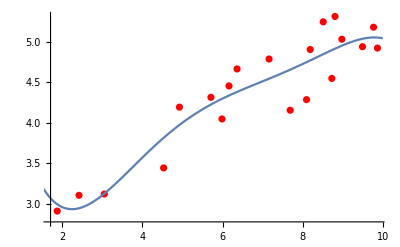

```mathematica
n=5;
line=Fit[data,x^#&/@Range[0,n],x];
Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,10}]]
```

```mathematica
Manipulate[line=Fit[data,x^#&/@Range[0,n],x];Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,10}]],{n,1,30}]
```

```mathematica
Manipulate[Factor[x^n+1],{{n,20},10,100,1}]
```

```mathematica
trainingSet={1->"A",2->"A",3.5->"B",5->"B"}
```

{1→A,2→A,3.5→B,5→B}

```mathematica
cf2=Classify[trainingSet]
```

```mathematica
digit=Classify[
{-Graphics-->2,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->2,-Graphics-->7,-Graphics-->5,-Graphics-->1,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->9,-Graphics-->6,-Graphics-->2,-Graphics-->8,-Graphics-->2,-Graphics-->0,-Graphics-->6,-Graphics-->6,-Graphics-->1,-Graphics-->1,-Graphics-->7,-Graphics-->8,-Graphics-->5,-Graphics-->0,-Graphics-->4,-Graphics-->7,-Graphics-->6,-Graphics-->0,-Graphics-->2,-Graphics-->5,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->6,-Graphics-->7,-Graphics-->5,-Graphics-->4,-Graphics-->1,-Graphics-->9,-Graphics-->3,-Graphics-->6,-Graphics-->8,-Graphics-->0,-Graphics-->9,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->7,-Graphics-->4,-Graphics-->4,-Graphics-->3,-Graphics-->8,-Graphics-->0,-Graphics-->4,-Graphics-->1,-Graphics-->3,-Graphics-->7,-Graphics-->6,-Graphics-->4,-Graphics-->7,-Graphics-->2,-Graphics-->7,-Graphics-->2,-Graphics-->5,-Graphics-->2,-Graphics-->0,-Graphics-->9,-Graphics-->8,-Graphics-->9,-Graphics-->8,-Graphics-->1,-Graphics-->6,-Graphics-->4,-Graphics-->8,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->6,-Graphics-->7,-Graphics-->4,-Graphics-->5,-Graphics-->8,-Graphics-->4,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->1,-Graphics-->9,-Graphics-->9,-Graphics-->9,-Graphics-->2,-Graphics-->4,-Graphics-->7,-Graphics-->3,-Graphics-->1,-Graphics-->9,-Graphics-->2,-Graphics-->9,-Graphics-->6}]
```

```mathematica
(1+2I)*(2+3I)
```

-4+7 ⅈ

```mathematica
Solve[x^2+2x+5==0,x]
```

{{x→-1-2 ⅈ},{x→-1+2 ⅈ}}

General::munfl: 3.14159/(1.40351251810153×10^419) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

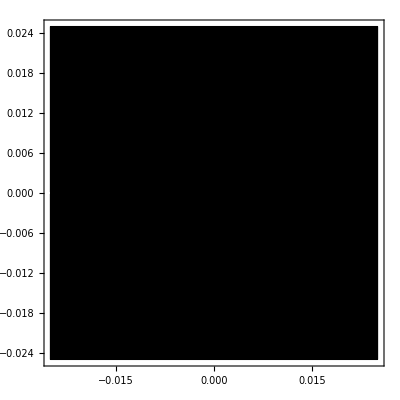

```mathematica
ComplexPlot[Exp[1/z^(3/2)],{z,-0.025-0.025I,0.025+0.025I},PlotLegends->Automatic]
```

```mathematica
ComplexPlot3D[(z^2+1)/(z^2-1),{z,-2-2I,2+2I}]
```

-Graphics3D-

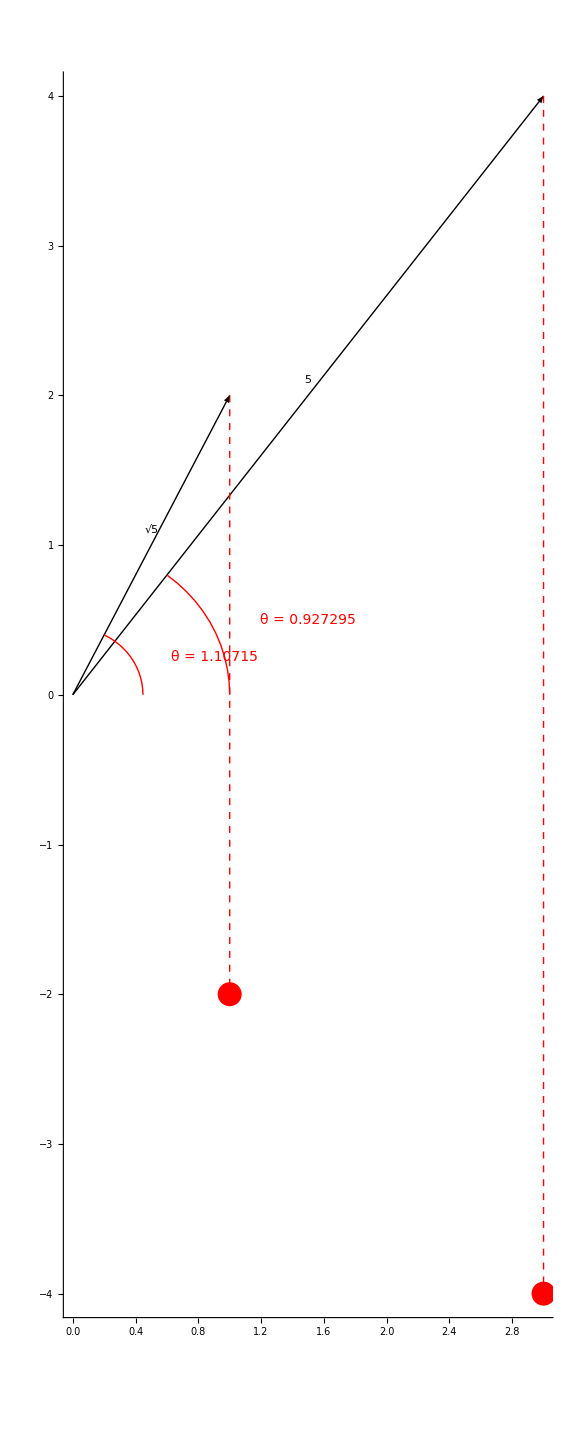

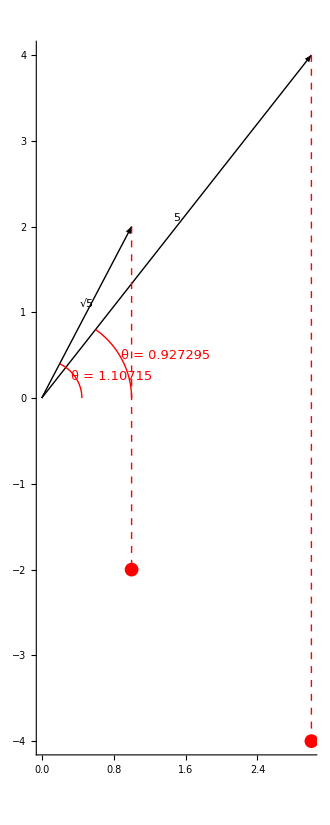

```mathematica
DrawComplex[c_]:=Graphics[{
Arrow[{{0,0},{Re[#],Im[#]}}&/@c],
{Dashed,Red,PointSize->.03,Point[{Re[Conjugate[#]],Im[Conjugate[#]]}&/@c]},
Inset[Norm[#],{.5*Re[#],.5*Im[#]+.1}]&/@c,
{Dashed,Red,Thick,Line[{{Re[#],Im[#]},{Re[#],-Im[#]}}&/@c]},
{Red,Thick,Circle[{0,0},Norm[#]/5,{0,Arg[#]}]&/@c},
Inset[Style["θ = "<>ToString[N[Arg[#]]],Red, Italic,14],({Re[#],Im[#]}+{Norm[#]+4,0})/8]&/@c
}, Axes->True,ImageSize->Large]
DrawComplex@{1+2I,3+4I}
```

```mathematica
1/(1+2I)
```

1/5-(2 ⅈ)/5

```mathematica
Conjugate[1+w
```

```mathematica
ⅇ^(Arg[#]I)&/@{1+2I}
```

{ⅇ^(ⅈ ArcTan[2])}